{{y[x]→InterpolatingFunction[…][x]}}

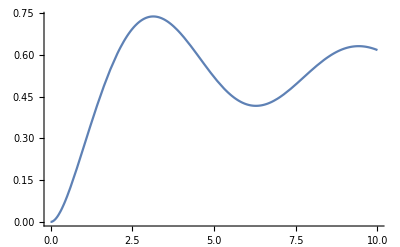

```mathematica
Clear["Global`*"]
s=NDSolve[{y'[x]==Sin[x]/(1+x+y[x]),y[0]==0},y[x],{x,0,10}]
Plot[Evaluate[y[x]/.s],{x,0,10},PlotRange->All]
```